# CoSyNE

for Mathematica

```mathematica
Row[{Style["Jan Koutnik, IDSIA, E-mail:  ",FontFamily->"Roman",FontSize->16],DynamicModule[{r="@"->".",bt,b=Button[bt,b=Hyperlink["mailto:"~~StringReplace[bt,{r,Reverse@r}]]]},bt="hkou.idsia@ch";Dynamic@b]}]
```

Jan Koutnik, IDSIA, E-mail:

Implemented according to the paper :

Faustino Gomez, Juergen Schmidhuber and Risto Miikkulainen (2008). Accelerated Neural Evolution through Cooperatively Coevolved Synapses. Journal of Machine Learning Research 9 (May), pp 937-965.

The current implementation uses only mutations (no crossover).The typical usage involves nesting coSyNeStep or coSyNeStepParallel function, see the examples.

## CoSyNE Functions

```mathematica
prependFitness[g_,fitFn_]:={fitFn[g],g}
```

```mathematica
newRandomPop[size_,n_,dist_,fitFn_]:=prependFitness[#,fitFn]&/@Table[RandomReal[dist],{size},{n}]
```

```mathematica
newRandomPopParallel[size_,n_,dist_,fitFn_]:=ParallelMap[prependFitness[#,fitFn]&,Table[RandomReal[dist],{size},{n}]]
```

```mathematica
conditionalPermutation[data_,pick_]:=ReplacePart[data,MapThread[Rule,{Flatten@Position[pick,True],RandomSample[Pick[data,pick]]}]];
```

```mathematica
sel[s_,g_]:=MapThread[{#2,#3}⟦#1⟧&,Prepend[g,s]]
```

```mathematica
uniformXover[g_]:=Module[{k,i},
i=NestList[3-#&,Table[RandomInteger[{1,2}],{Length[g⟦1⟧]}],1];
Map[sel[#,g]&,i]
]
```

```mathematica
cauchyPerturbation[x_]:=x+RandomReal[CauchyDistribution[0,0.3]]
```

```mathematica
cauchyMutate[g_,mprob_]:=MapAt[cauchyPerturbation,g,Position[Sign[RandomReal[{0,1},{Length[g]}]-mprob],-1]]
```

```mathematica
xoverIndividuals[indiv_,fitnessFn_,mprob_]:=Module[{g=indiv⟦All,2⟧,res},
prependFitness[#,fitnessFn]&/@(cauchyMutate[#,mprob]&/@uniformXover[g])
]
```

```mathematica
evolutionStep[pop_,fitFn_,OptionsPattern[{mutate->0.5,minimize->False,permuteAll->False,verbose->False,elite->0}]]:=Module[{fp=Sort[pop],p2,fmin,fmax,g2,t,r,res,perm,n=Length[Last@First@pop],fit,tbl,mprob=OptionValue[mutate],el,newIndiv2,newFit2},
(*Reverse if maximizing*)
If[¬OptionValue[minimize],fp=Reverse@fp];
(*store elite*)
el=fp⟦1;;OptionValue[elite]⟧;
(*take the top quarter and mutate it twice to get one half size of new individuals*)
p2=mapFn[prependFitness[#,fitFn]&,(cauchyMutate[#,mprob]&/@Join[fp⟦1;;Length[fp]/4⟧,fp⟦1;;Length[fp]/4⟧]⟦All,2⟧)];
(*take the original genomes and their fitness separately*)
g2=fp⟦All,2⟧;fit=First/@fp;
(*compute the poermutations probabilities*)
t=ParallelTable[Power[Rescale[fit⟦i⟧,#@@(First/@fp)&/@{Min,Max}],1/n],{i,Length[pop]}];
(*for maximizing, 1 - probabilities, such that bests are les permuted*)
If[¬OptionValue[minimize],t=1-t];
(*generate random binary numbers*)
r=RandomReal[{0,1},{Length[pop]}];
(*generate permutation pattern, for elitism, use 0 in the beg.*)
If[OptionValue[permuteAll],perm=ParallelTable[True,{Length[pop]}],perm=Sign[t-r]/.{-1->False,1->True}];
(*permutate the old ones, join the new ones, sort*)
newIndiv2=Transpose[ParallelMap[conditionalPermutation[#1,perm]&,g2ᵀ]];
res=Sort@Join[el,mapFn[prependFitness[#,fitFn]&,newIndiv2],p2];
(*reverse if maximizing*)
If[¬OptionValue[minimize],res=Reverse@res];
(*cut off the worst*)
If[OptionValue[verbose],PrintTemporary[Round[#,0.001]&/@res⟦1;;Length[pop],1⟧]];
res⟦1;;Length[pop]⟧
]
```

Serial evaluation wrapper:

```mathematica
coSyNEstep[pop_,fitFn_,opts:OptionsPattern[{mutate->0.5,minimize->False,permuteAll->False,verbose->False,elite->0}]]:=Block[{mapFn=Map},evolutionStep[pop,fitFn,opts]]
```

Parallel evaluation wrapper :

```mathematica
coSyNEstepParallel[pop_,fitFn_,opts:OptionsPattern[{mutate->0.5,minimize->False,permuteAll->False,verbose->False,elite->0}]]:=Block[{mapFn=ParallelMap},evolutionStep[pop,fitFn,opts]]
```

Prioritized parallel evaluationwrapper (bigger instances get evaluated first) :

```mathematica
prioritizedParallelMap[fn_,x_]:=With[{ord=Reverse[Ordering[rankFn/@x]]},ParallelMap[fn,x⟦ord⟧]⟦ord⟧]
```

```mathematica
coSyNEstepPrioritizedParallel[pop_,fitFn_,rankingFn_,opts:OptionsPattern[{mutate->0.5,minimize->False,permuteAll->False,verbose->False,elite->0}]]:=Block[{mapFn=prioritizedParallelMap,rankFn=rankingFn},evolutionStep[pop,fitFn,opts]]
```

## Examples

Simple experiment that compares cosyne with standard direct encoding evolution. Fitness function is the sum of absolute gene values (L1-norm), which is minimized (search for the zero vector).

```mathematica
fitFn[g_]:=Norm[g,1]
```

Populatin with 16 individuals, each has 5 genes.

```mathematica
pop=newRandomPop[16,5,NormalDistribution[0,1],fitFn];
```

50 evolution steps repeated 20 times for cosyne and non - cosyne.

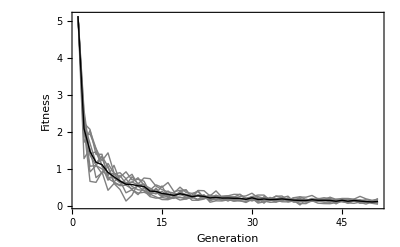

```mathematica
c=Table[First/@First/@
NestList[coSyNEstep[#,fitFn,minimize->True,mutate->0.8,permuteAll->True,verbose->False,elite->0]&,pop,
50],{10}];

Show[{ListLinePlot[c,PlotStyle->Gray,PlotRange->All,ImageSize->400,FrameLabel->{"Generation","Fitness"},AxesOrigin->{0,0},Frame->True],ListLinePlot[Mean[c],PlotRange->All,PlotStyle->{Thick,Black}]}]
```

The same example using 1 elite individual

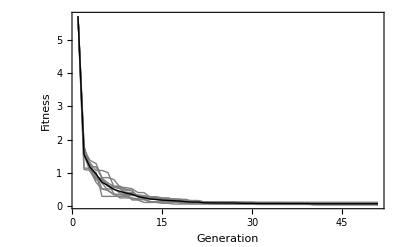

```mathematica
c=Table[First/@First/@
NestList[coSyNEstep[#,fitFn,minimize->True,mutate->0.8,permuteAll->True,verbose->False,elite->1]&,pop,
50],{10}];

Show[{ListLinePlot[c,PlotStyle->Gray,PlotRange->All,ImageSize->400,FrameLabel->{"Generation","Fitness"},AxesOrigin->{0,0},Frame->True],ListLinePlot[Mean[c],PlotRange->All,PlotStyle->{Thick,Black}]}]
```

Probabilistic permutation (individuals with best rank have low probability of being permuted -- the elity is not needed):

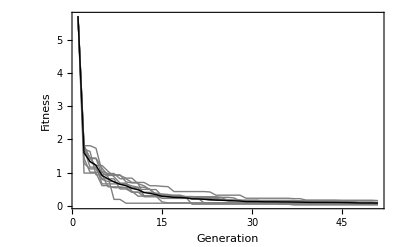

```mathematica
c=Table[First/@First/@
NestList[coSyNEstep[#,fitFn,minimize->True,mutate->0.8,permuteAll->False,verbose->False,elite->0]&,pop,
50],{10}];

Show[{ListLinePlot[c,PlotStyle->Gray,PlotRange->All,ImageSize->400,FrameLabel->{"Generation","Fitness"},AxesOrigin->{0,0},Frame->True],ListLinePlot[Mean[c],PlotRange->All,PlotStyle->{Thick,Black}]}]
```